# Modelling and Control of One Leg Hopper

## Diagram

```mathematica
Graphics[{Thick,Green,Rectangle[{-0.3,-0.1},{0.3,0.1}],Thick,Blue,Line[{{0,0},{Sin[Pi/6],-Cos[Pi/6]}}], Thick, Blue,Disk[{Sin[Pi/6],-Cos[Pi/6]},0.05], Thick,Blue,Line[{{Sin[Pi/6],-Cos[Pi/6]},{Sin[Pi/6]+Sin[Pi/6-Pi/3],-Cos[Pi/6]-Cos[Pi/6-Pi/3]}}], Disk[{Sin[Pi/6]+Sin[Pi/6-Pi/3],-Cos[Pi/6]-Cos[Pi/6-Pi/3]},0.05]}]
```

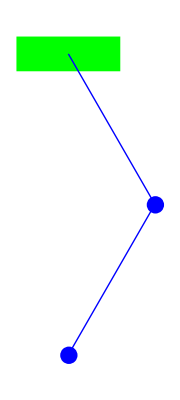

After simulating the simpler dynamics of systems like the pendulum and the cart pole, we are now moving ahead to the simulation of the dynamics of a small part of the final robot. I am making the assumption that the final robot will resemble four sections like the one pictured above connected together rigidly (at first) and eventually with a flexible spine. In this Mathematica notebook I will, using the Lagrangian of the system, get the equations of the dynamics of the system. These equations can be used both to mathematically model the system and to develop a model based controller.

## Writing Down the Lagrangian

```mathematica
ClearAll["Global`*"];
T[t_]=1/2 M0 (x'[t]^2+y'[t]^2) + 1/2 M1((l1 θ1'[t]Cos[θ1[t]]+x'[t])^2 + (l1 θ1'[t]Sin[θ1[t]]+y'[t])^2)+1/2 M2 ((l2 θ2'[t]Cos[θ1[t]+θ2[t]]+l1 θ1'[t]Cos[θ1[t]]+x'[t])^2+(l2 θ2'[t]Sin[θ1[t] + θ2[t]]+l1 θ1'[t]Sin[θ1[t]]+y'[t])^2);
V[t_]=M0 g y[t] + M1 g(y[t]-l1 Cos[θ1[t]]) + M2(y[t]-l1 Cos[θ1[t]]-l2 Cos[θ1[t]+θ2[t]]);
L[t_]=T[t]-V[t];
```

## Solving Dynamics Using Euler-Lagrange

```mathematica
dynamics = Expand[{D[D[L[t],x'[t]],t] - D[L[t],x[t]], D[D[L[t],y'[t]],t] - D[L[t],y[t]], D[D[L[t],θ1'[t]],t] - D[L[t],θ1[t]], D[D[L[t],θ2'[t]],t] - D[L[t],θ2[t]]}]
```

{-l1 M1 Sin[θ1[t]] θ1'[t]^2-l1 M2 Sin[θ1[t]] θ1'[t]^2-l2 M2 Sin[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-l2 M2 Sin[θ1[t]+θ2[t]] θ2'[t]^2+M0 x''[t]+M1 x''[t]+M2 x''[t]+l1 M1 Cos[θ1[t]] θ1''[t]+l1 M2 Cos[θ1[t]] θ1''[t]+l2 M2 Cos[θ1[t]+θ2[t]] θ2''[t],g M0+g M1+M2+l1 M1 Cos[θ1[t]] θ1'[t]^2+l1 M2 Cos[θ1[t]] θ1'[t]^2+l2 M2 Cos[θ1[t]+θ2[t]] θ1'[t] θ2'[t]+l2 M2 Cos[θ1[t]+θ2[t]] θ2'[t]^2+M0 y''[t]+M1 y''[t]+M2 y''[t]+l1 M1 Sin[θ1[t]] θ1''[t]+l1 M2 Sin[θ1[t]] θ1''[t]+l2 M2 Sin[θ1[t]+θ2[t]] θ2''[t],g l1 M1 Sin[θ1[t]]+l1 M2 Sin[θ1[t]]+l2 M2 Sin[θ1[t]+θ2[t]]+l2 M2 Sin[θ1[t]+θ2[t]] x'[t] θ2'[t]-l2 M2 Cos[θ1[t]+θ2[t]] y'[t] θ2'[t]+l1 l2 M2 Cos[θ1[t]+θ2[t]] Sin[θ1[t]] θ2'[t]^2-l1 l2 M2 Cos[θ1[t]] Sin[θ1[t]+θ2[t]] θ2'[t]^2+l1 M1 Cos[θ1[t]] x''[t]+l1 M2 Cos[θ1[t]] x''[t]+l1 M1 Sin[θ1[t]] y''[t]+l1 M2 Sin[θ1[t]] y''[t]+l1^2 M1 Cos[θ1[t]]^2 θ1''[t]+l1^2 M2 Cos[θ1[t]]^2 θ1''[t]+l1^2 M1 Sin[θ1[t]]^2 θ1''[t]+l1^2 M2 Sin[θ1[t]]^2 θ1''[t]+l1 l2 M2 Cos[θ1[t]] Cos[θ1[t]+θ2[t]] θ2''[t]+l1 l2 M2 Sin[θ1[t]] Sin[θ1[t]+θ2[t]] θ2''[t],l2 M2 Sin[θ1[t]+θ2[t]]-l2 M2 Sin[θ1[t]+θ2[t]] x'[t] θ1'[t]+l2 M2 Cos[θ1[t]+θ2[t]] y'[t] θ1'[t]+l2 M2 Cos[θ1[t]+θ2[t]] x''[t]+l2 M2 Sin[θ1[t]+θ2[t]] y''[t]+l1 l2 M2 Cos[θ1[t]] Cos[θ1[t]+θ2[t]] θ1''[t]+l1 l2 M2 Sin[θ1[t]] Sin[θ1[t]+θ2[t]] θ1''[t]+l2^2 M2 Cos[θ1[t]+θ2[t]]^2 θ2''[t]+l2^2 M2 Sin[θ1[t]+θ2[t]]^2 θ2''[t]}

```mathematica
M0=1;
M1=1;
M2=1;
l1=1;
l2=1;
g=9.81;
```

```mathematica
sol= NDSolve[{dynamics[[1]]==0,dynamics[[2]]==0,dynamics[[3]]==(θ2[t]-Pi/6),dynamics[[4]]==(θ1[t]+Pi/3),x[0]==0,y[0]==3,θ1[0]==Pi/6,θ2[0]==-Pi/3,x'[0]==0,y'[0]==0,θ1'[0]==0,θ2'[0]==0},{x,y,θ1,θ2},{t,0,10}]
```

{{x→InterpolatingFunction[{{0., 10.}}, <>],y→InterpolatingFunction[{{0., 10.}}, <>],θ1→InterpolatingFunction[{{0., 10.}}, <>],θ2→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
xs=Part[sol[[1,All,-1]],1];
ys=Part[sol[[1,All,-1]],2];
θ1s=Part[sol[[1,All,-1]],3];
θ2s=Part[sol[[1,All,-1]],4];
Animate[Graphics[{Thick,Green,Rectangle[{xs[t]-0.3,ys[t]-0.1},{xs[t]+0.3,ys[t]+0.1}],Thick,Blue,Line[{{xs[t],ys[t]},{xs[t]+l1 Sin[θ1s[t]],ys[t]-l1 Cos[θ1s[t]]},{xs[t]+l1 Sin[θ1s[t]]+l2 Sin[θ1s[t]+θ2s[t]], ys[t]-l1 Cos[θ1s[t]]-l2 Cos[θ1s[t]+θ2s[t]]}}]},Axes->True,AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}],{t,0,10},AnimationRunning->False]
```